```mathematica
B=0.5
```

0.5

```mathematica
ArcTan[(x2-x0)/2,(2*x1-x0-x2)/2]{x0,x1,x2}
```

{-(-x0+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))-(x0-2 x1+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)),(-x0+x2)/(2 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)),-(-x0+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))+(x0-2 x1+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))}

```mathematica
√((-(-x0+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))-(x0-2 x1+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)))^2*d0^2+((-x0+x2)/(2 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)))^2*d1^2+(-(-x0+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))+(x0-2 x1+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)))^2*d2^2)
```

√((d1^2 (-x0+x2)^2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)^2)+d0^2 (-(-x0+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))-(x0-2 x1+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)))^2+d2^2 (-(-x0+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2))+(x0-2 x1+x2)/(4 (1/4 (-x0+2 x1-x2)^2+1/4 (-x0+x2)^2)))^2)

```mathematica
Simplify[%2]
```

√((d2^2 (x0-x1)^2+d1^2 (x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
Simplify[%16]
```

```mathematica
√((d1^2 *(x0-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

```mathematica
√((d2^2 (x0-x1)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

```mathematica
√((d2^2 (x0-x1)^2+d1^2 *(x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

```mathematica
ERROR=√((d2^2 (x0-x1)^2+d1^2 (x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

√((d2^2 (x0-x1)^2+d1^2 (x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
√((((1-x2)*x2)/100* (x0-x1)^2+((1-x1)*x1)/100* (x0-x2)^2+((1-x0)*x0)/100* (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

√((1/100 (1-x1) x1 (x0-x2)^2+1/100 (1-x0) x0 (x1-x2)^2+1/100 (x0-x1)^2 (1-x2) x2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
Simplify[√((1/100 (1-x1) x1 (x0-x2)^2+1/100 (1-x0) x0 (x1-x2)^2+1/100 (x0-x1)^2 (1-x2) x2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))]
```

1/10 √((x1 x2 (x1+x2-2 x1 x2)+x0^2 (x1-2 x1^2+x2+2 x1 x2-2 x2^2)+x0 (2 x1 (-3+x2) x2+x2^2+x1^2 (1+2 x2)))/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
d0^2=((1-x0)*x0)/100
d1^2=((1-x1)*x1)/100
```

```mathematica
d2^2=((1-x2)*x2)/100
```

```mathematica
x0=(A*Cos[φ]+B)
```

```mathematica
x1=(-A*Sin[φ]+B)
```

```mathematica
x2=(-A*Cos[φ]+B)
```

```mathematica
√((((1-(-A*Cos[φ]+B))*(-A*Cos[φ]+B))/100*((A*Cos[φ]+B)-(-A*Sin[φ]+B))^2+((1-(-A*Sin[φ]+B))*(-A*Sin[φ]+B))/100* ((A*Cos[φ]+B)-(-A*Cos[φ]+B))^2+((1-(A*Cos[φ]+B))*(A*Cos[φ]+B))/100*((-A*Sin[φ]+B)-(-A*Cos[φ]+B))^2)/((A*Cos[φ]+B)^2-2 *(A*Cos[φ]+B)* (-A*Sin[φ]+B)+2 *(-A*Sin[φ]+B)^2-2 *(-A*Sin[φ]+B)* (-A*Cos[φ]+B)+(-A*Cos[φ]+B)^2)^2)
```

√((1/100 (1-B-A Cos[φ]) (B+A Cos[φ]) (A Cos[φ]-A Sin[φ])^2+1/25 A^2 Cos[φ]^2 (B-A Sin[φ]) (1-B+A Sin[φ])+1/100 (B-A Cos[φ]) (1-B+A Cos[φ]) (A Cos[φ]+A Sin[φ])^2)/((B-A Cos[φ])^2+(B+A Cos[φ])^2-2 (B-A Cos[φ]) (B-A Sin[φ])-2 (B+A Cos[φ]) (B-A Sin[φ])+2 (B-A Sin[φ])^2)^2)

```mathematica
Simplify[%1]
```

(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B-4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)

```mathematica
B=0.5
```

0.5

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B-4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

(√(-(A^2 Cos[φ]^4-0.25 Sin[φ]^2+Cos[φ]^2 (-0.75+3 A^2 Sin[φ]^2))/A^2))/(10 √2)

```mathematica
Simplify[%21]
```

√((0.00375 Cos[φ]^2)/A^2-0.005 Cos[φ]^4+(0.00125 Sin[φ]^2)/A^2-0.00375 Sin[2 φ]^2)

```mathematica
g=Plot3D[{Legended[(√(-(A^2 Cos[φ]^4-0.25 Sin[φ]^2+Cos[φ]^2 (-0.75+3 A^2 Sin[φ]^2))/A^2))/(10 √2),"Error Plot"]},{A,0,0.45},{φ,-Pi,Pi},AxesLabel->{A,φ,dφ}]
```

-Graphics3D-

```mathematica
N=20
```

20

```mathematica
f[x_]:=x/N
```

```mathematica
Array[f,20,0]
```

{0,1/N,2/N,3/N,4/N,5/N,6/N,7/N,8/N,9/N,10/N,11/N,12/N,13/N,14/N,15/N,16/N,17/N,18/N,19/N}

```mathematica
N=20
```

20

```mathematica
{0,1/N,2/N,3/N,4/N,5/N,6/N,7/N,8/N,9/N,10/N,11/N,12/N,13/N,14/N,15/N,16/N,17/N,18/N,19/N}
```

{0,1/N,2/N,3/N,4/N,5/N,6/N,7/N,8/N,9/N,10/N,11/N,12/N,13/N,14/N,15/N,16/N,17/N,18/N,19/N}

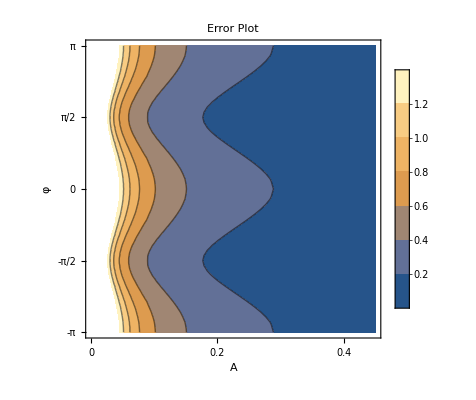

```mathematica
g=ContourPlot[√((0.00375 Cos[φ]^2)/A^2-0.005 Cos[φ]^4+(0.00125 Sin[φ]^2)/A^2-0.00375 Sin[2 φ]^2),{A,0,0.45},{φ,-Pi,Pi},PlotLabel->"Error Plot",FrameTicks->{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{-Pi,-Pi/2,0,Pi/2,Pi}},AxesLabel->{A,φ},PlotLegends->Automatic]
```

```mathematica
√((((1-(-A*Cos[φ]+B))*(-A*Cos[φ]+B))/100*((A*Cos[φ]+B)-(A*Sin[φ]+B))^2+((1-(A*Sin[φ]+B))*(A*Sin[φ]+B))/100* ((A*Cos[φ]+B)-(-A*Cos[φ]+B))^2+((1-(A*Cos[φ]+B))*(A*Cos[φ]+B))/100*((A*Sin[φ]+B)-(-A*Cos[φ]+B))^2)/((A*Cos[φ]+B)^2-2 *(A*Cos[φ]+B)* (A*Sin[φ]+B)+2 *(A*Sin[φ]+B)^2-2 *(A*Sin[φ]+B)* (-A*Cos[φ]+B)+(-A*Cos[φ]+B)^2)^2)
```

√((1/100 (B-A Cos[φ]) (1-B+A Cos[φ]) (A Cos[φ]-A Sin[φ])^2+1/25 A^2 Cos[φ]^2 (1-B-A Sin[φ]) (B+A Sin[φ])+1/100 (1-B-A Cos[φ]) (B+A Cos[φ]) (A Cos[φ]+A Sin[φ])^2)/((B-A Cos[φ])^2+(B+A Cos[φ])^2-2 (B-A Cos[φ]) (B+A Sin[φ])-2 (B+A Cos[φ]) (B+A Sin[φ])+2 (B+A Sin[φ])^2)^2)

```mathematica
Simplify[%1]
```

(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)

```mathematica
data=Table[(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2),{A,0.01,1,0.01},{B,0.01,1,0.01},{φ,-Pi,Pi,0.01}]
```

{{{1.21655,1.20843,1.20018,1.19179,621,1.24252,1.23486,1.22706,1.21911},98,{1}},98,{1}}
 |  |  |  |

```mathematica
ListDensityPlot3D[data,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,1},{-Pi,Pi}},PlotLegends->Automatic,AxesLabel->{A,B,φ}]
```

-Graphics3D-

```mathematica
P=(1+cos(w-Subscript[w, 0])t)/2
```

```mathematica
P/w=t*((-sin(w-Subscript[w, 0])t)/2)
```

```mathematica
Subscript[w, 0] = 13.44657262
```

for h = 1, we have [ 0.5001576   0.99968619 13.44657262 10.9956268 ]
for h = 1.01, we have [ 0.50009912  0.99980453 13.58089893  4.71236935]
for h = 0.99, we have [ 0.50025409  0.99949689 13.31170223  4.71238118]

```mathematica
13.58089893-13.31170223
```

0.269197

```mathematica
500/8
```

125/2

```mathematica
N[125/2]
```

```mathematica
62.5*0.0002
```

0.0125

```mathematica
9+1.20
```

```mathematica
10.2/10
```

```mathematica
1.02*500*0.0002
```

0.102